# Linearity

```mathematica
theoreticalColor="TropicalRainForest";
experimentalColor="Bittersweet";
lineFitColor = "Green";
histogramColor="Asparagus";
zeroFreqColor="Razzmatazz";
zeroFreqColorAtF = "ShamRock";
```

```mathematica
vrrrangemax=19.58537402425683;
lineStyle={Thickness[0.005],ColorData["Crayola"]["Purple"],Dashed};
lineK=Line[{{vrrrangemax,0},{vrrrangemax,1.1}}];
```

## Observation

```mathematica
experimentalList={{0.5,23/1000},{1,47/1000},{1.67, 78/1000},{2,95/1000 },{3,169/1000},{4,193/1000},{5,233/1000},{6,288/1000},{7,315/1000},{8,391/1000},{9,441/1000},{10,469/1000},{11, 559/1000},{12, 602/1000},{13, 637/1000},{14,714/1000},{15,774/1000},{16, 839/1000},{16.7, 893/1000},{17,912/1000},{18,957/1000},{19,989/1000},{20,997/1000}};
experimentalList={{1.67, 78/1000},{2,95/1000 },{3,169/1000},{4,193/1000},{5,233/1000},{6,288/1000},{7,315/1000},{8,391/1000},{9,441/1000},{10,469/1000},{11, 559/1000},{12, 602/1000},{13, 637/1000},{14,714/1000},{15,774/1000},{16, 839/1000},{17,912/1000},{18,957/1000},{19,989/1000},{20,997/1000}};
experimentalListForErrorPlot={{1.67, 78/1000},{2,95/1000 },{3,169/1000},{4,193/1000},{5,233/1000},{6,288/1000},{7,315/1000},{8,391/1000},{9,441/1000},{10,469/1000},{12, 602/1000},{13, 637/1000},{15,774/1000},{16, 839/1000},{17,912/1000},{18,957/1000},{19,989/1000}};
experimentalListFunc = Interpolation[experimentalList];
```

```mathematica
experimentalListFunc [15.2]
```

0.786504

```mathematica
experimentalList95CIUpper=experimentalList;
experimentalList95CILower=experimentalList;
```

https://en.wikipedia.org/wiki/Binomial_proportion_confidence_interval

```mathematica
For[i=1,i<=Length[experimentalList], i++,experimentalList95CIUpper[[i]][[2]] =experimentalList[[i]][[2]] + 1.96*Sqrt[experimentalList[[i]][[2]]*(1-experimentalList[[i]][[2]])]/Sqrt[1000]]
```

```mathematica
For[i=1,i<=Length[experimentalList], i++,experimentalList95CILower[[i]][[2]] =experimentalList[[i]][[2]] - 1.96*Sqrt[experimentalList[[i]][[2]]*(1-experimentalList[[i]][[2]])]/Sqrt[1000]]
```

```mathematica
ConfidenceBand={};
```

```mathematica
For[i=1,i<=Length[experimentalList], i++,{ConfidenceBand=Append[ConfidenceBand,{0,0}],ConfidenceBand[[i]][[1]]=experimentalList95CILower[[i]][[2]],ConfidenceBand[[i]][[2]]=experimentalList95CIUpper[[i]][[2]]}]
```

```mathematica
ConfidenceBand;
```

```mathematica
list=Table[Around[experimentalList[[n]][[2]],1.96*Sqrt[experimentalList[[n]][[2]]*(1-experimentalList[[n]][[2]])]/Sqrt[1000]],{n,1,Length[experimentalList],1}];
```

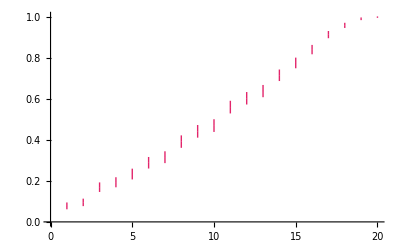

```mathematica
barplot=ListPlot[list,IntervalMarkers->"Bars",PlotStyle->{ColorData["Crayola"]["Razzmatazz"],PointSize[0.001]}]
```

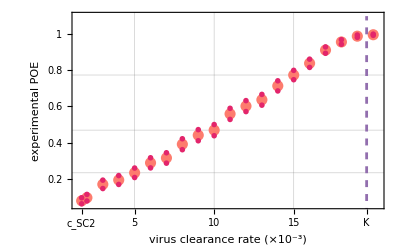

```mathematica
p1=ListPlot[
{experimentalList, experimentalList95CILower, experimentalList95CIUpper},
PlotStyle->{{ColorData["Crayola"][experimentalColor],PointSize[0.02]}, {ColorData["Crayola"]["Razzmatazz"],PointSize[0.01]}, {ColorData["Crayola"]["Razzmatazz"],PointSize[0.01]}},
FrameLabel->{Row[{"virus clearance rate   (", Style["×10^-3", 26],")"}],"experimental POE"},PlotTheme->"Scientific",LabelStyle->Directive[FontFamily->"Times",Black,FontSize->30],
PlotRange->{{1.44,20.3},{0.055,1.1}},
TicksStyle->Medium,
GridLines->{{0,5,10,15}, Map[experimentalListFunc[#] &, {5,10,15}]},
FrameTicks->{
{{ {0, "0   "}, 0.2, 0.4, 0.6, 0.8, {1, "1   "}},None},
{{{1.67, Subscript["c","SC2"]},5,10,15, {vrrrangemax, "K"}},None}},
Epilog->{Directive[lineStyle],lineK},
ImageSize->Scaled[0.4]]
```

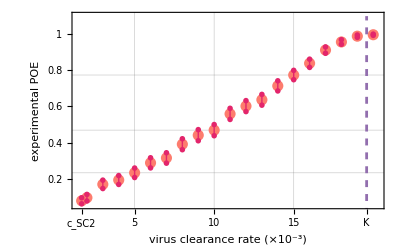

```mathematica
Show[p1,barplot]
```

```mathematica
lineFit=Fit[experimentalList,{x},x]
```

0.0510585 x

```mathematica
lineFitOriginal=Fit[experimentalList,{1,x},x]
```

-0.0229885+0.0527449 x

```mathematica
myLinearFunction[x_]:=0.05105850921006065 x
```

```mathematica
avg = N[Sum[experimentalList[[i]][[2]],{i,1,Length[experimentalList]}]/Length[experimentalList]]
```

0.5326

```mathematica
1-Sum[(experimentalList[[i]][[2]] - myLinearFunction[experimentalList[[i]][[1]]])^2,{i,1,Length[experimentalList]}]/Sum[(experimentalList[[i]][[2]] - avg)^2,{i,1,Length[experimentalList]}]
```

0.993862

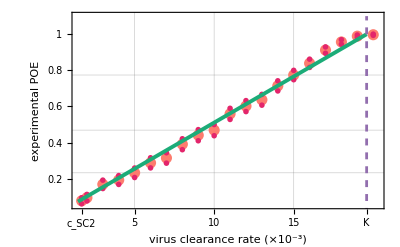

```mathematica
p2 =Show[
p1,
Plot[lineFit,{x,1.44,vrrrangemax}, PlotStyle->{ColorData["Crayola"][lineFitColor ],Thickness[0.007]}]]
```

```mathematica
Solve[lineFit==1,x]
```

{{x→19.5854}}

note: for the majority of the curve above we see ~reasonable linearity, the end seems mollified. Towards the end (vrr = 19, 20) we don’t really have E(X)>>1, so the fix point theorem does not hold in itself. (and it is the fix point theorem that gives us linearity at this point)

## Offspring distribution

#### Virus removal rate \in [1.67 , 18] * E-3

```mathematica
VRRString = "2";
VRRNumString="2";
```

```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo"<>VRRString<>".txt", "Table"];
```

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0}}

```mathematica
Length[cleanData]
```

1000

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,89},{1,78},{2,73},{3,58},{4,65},{5,51},{6,57},{7,55},{8,54},{9,35},{10,23},{11,30},{12,35},{13,35},{14,17},{15,23},{16,25},{17,23},{18,12},{19,6},{20,18},{21,15},{22,9},{23,17},{24,7},{25,12},{26,7},{27,5},{28,7},{29,9},{30,5},{31,3},{32,8},{33,1},{34,3},{35,3},{36,1},{37,8},{38,1},{39,3},{40,3},{41,2},{42,1},{43,0},{44,1},{45,0},{46,0},{47,0},{48,1},{49,1},{50,0},{51,1},{52,0},{53,0},{54,0},{55,1},{56,0},{57,0},{58,1},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,1},{66,1}}

check if the expected value is > 1 (it is a condition in the fix point theorem)

```mathematica
ExpectedValueOffspring=N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

9.938

```mathematica
N[Sum[(cleanData[[i]]-ExpectedValueOffspring)^2,{i,1,Length[cleanData]}]]/1000
```

96.3042

```mathematica
(1-0.476)/(0.476^2)
```

2.31269

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartStyle->ColorData["Crayola"]["GrannySmithApple"],PlotLabel->"VRR="<>VRRNumString<>"E-3. Shown against geometric distr., Freq. Zero"];
```

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[probabilityData[[1,2]]/1000],x]//Evaluate,{x,0,Max[cleanData]},
PlotStyle->ColorData["Crayola"]["PineGreen"],
PlotMarkers->Automatic];
```

```mathematica
probabilityData[[1,2]]/1000 //N
```

0.089

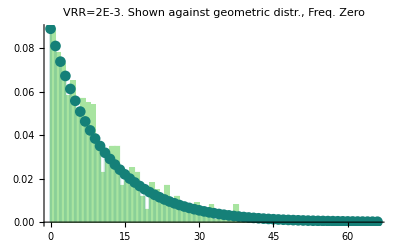

```mathematica
Show[p1,p2]
```

Gábor ötlete: geom param: mintaátlag reciproka, ML becslés; K-S próba.
Végeredmény: melyik param becslés ad jobb illeszkedést.

```mathematica
geoParamMLE=1/(Mean[cleanData]+1)
```

0.0914244

```mathematica
Max[cleanData]
```

66.

```mathematica
geoParamMLE
```

0.0914244

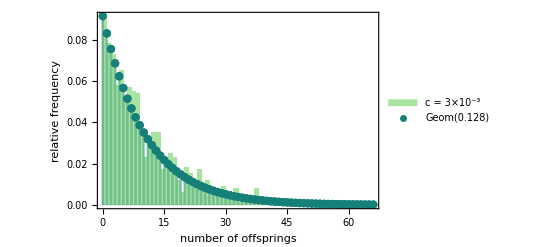

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartStyle->ColorData["Crayola"]["GrannySmithApple"],FrameLabel->{Row[{"number of offsprings"}],"relative frequency"},PlotTheme->"Scientific",
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->30],
ChartLegends->{Placed[{"c = 3×10^-3"},{0.718,0.8}]},
TicksStyle->Medium,ImageSize->Scaled[0.5]];
p2=DiscretePlot[PDF[GeometricDistribution[geoParamMLE],x]//Evaluate,{x,0,Max[cleanData]},
PlotStyle->{ColorData["Crayola"]["PineGreen"],PointSize[0.015]},PlotLegends->{Placed[PointLegend[{" "},LegendMarkerSize->Medium, LegendMarkers->Automatic],{0.591,0.65}]},LabelStyle->Directive[FontFamily->"Times",Black,FontSize->30]];
p3=DiscretePlot[PDF[GeometricDistribution[geoParamMLE],x]//Evaluate,{x,0,Max[cleanData]},
PlotStyle->{ColorData["Crayola"]["PineGreen"],PointSize[0.015]},PlotLegends->{Placed[PointLegend[{"Geom(0.128)"},LegendMarkerSize->0.000000001, LegendMarkers->Automatic],{0.729,0.63}]},LabelStyle->Directive[FontFamily->"Times",Black,FontSize->30]];
Show[p1,p2,p3]
```

Observation: we seem to have a reasonable fit to geometric distribution, where the distribution’s only parameter is set to the relative frequency of 0 offsprings. This holds for a wide range of VRR values, not just mu=3.

#### Virus removal rate = very small, i.e. 0.5*E-3

```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo0dot5.txt", "Table"];
```

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=2,i<=2*dataLength, i=i+2,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData;
```

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData;
```

check if the expected value is > 1 (it is a condition in the fix point theorem)

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

40.463

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartLegends->{"Offspring histogram, VRR=3*E-3."},ChartStyle->"Pastel",PlotLabel->"Shown against geometric distr."];
```

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[probabilityData[[1,2]]/1000],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

```mathematica
geoParamMLE=1/(Mean[cleanData]+1)
```

0.0241179

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[geoParamMLE],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

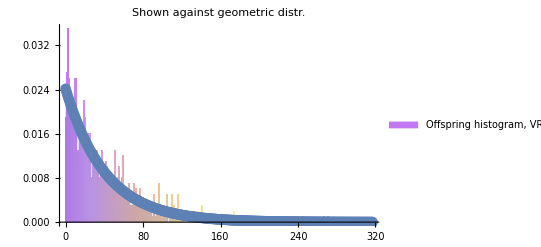

```mathematica
Show[p1,p2]
```

Observation: we seem to have a reasonable fit to geometric distribution, where the distribution’s only parameter is set to the relative frequency of 0 offsprings. This holds for a wide range of VRR values, not just mu=3.

## The Maximum Likelihood estimate of the parameter of the geometric distribution.

```mathematica
vrrrangemax
```

19.5854

MLE list with and without 20:

```mathematica
MLEstList={{0.5, 0.024},{1.67,0.07431},{2.0,0.091424},{3,0.128617},{4,0.167476},{5,0.1970055},{6,0.219202104340201},{7,0.26752273},{8,0.27708506},{9,0.318167},{10,0.3246753},{11,0.338180},{12,0.386548},{13,0.392772},{14,0.40883},{15,0.443852},{16,0.447227},{16.7, 0.468603},{17,0.461467},{18,0.47664},{20,0.5112474}};
MLEstList={{1.67,0.07431},{2.0,0.091424},{3,0.128617},{4,0.167476},{5,0.1970055},{6,0.219202104340201},{7,0.26752273},{8,0.27708506},{9,0.318167},{10,0.3246753},{11,0.338180},{12,0.386548},{13,0.392772},{14,0.40883},{15,0.443852},{16,0.447227},{17,0.461467},{18,0.47664},{19, 0.486618}};
MLEstListFunc = Interpolation[MLEstList];
```

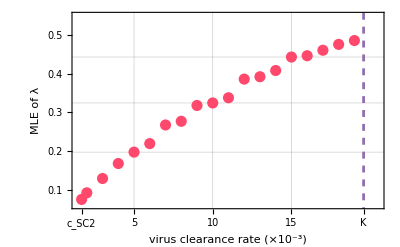

```mathematica
p3=ListPlot[
MLEstList,
PlotStyle->{ColorData["Crayola"]["RadicalRed"],PointSize[0.02]},
FrameLabel->{Row[{"virus clearance rate   (", Style["×10^-3", 24],")"}],"MLE of λ"},PlotTheme->"Scientific",LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
PlotRange->{{1.44,20.5},{0.06,0.55}},
TicksStyle->Medium,
GridLines->{{5,10,15}, Map[MLEstListFunc[#] &, {5,10,15}]},
FrameTicks->{
{{ 0.1, 0.2, 0.3, 0.4, 0.5},None},
{{{1.67, Subscript["c","SC2"]},5,10,15, {vrrrangemax, "K"}},None}},
Epilog->{Directive[lineStyle],lineK},
ImageSize->Scaled[0.4]]
```

This looks similar to part of the 1/(1+(a/x)^n) curve -- Hill equation with n=1:

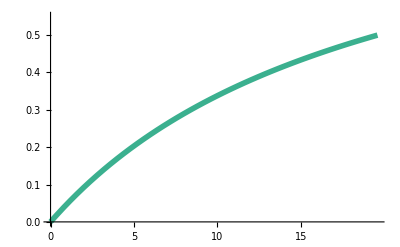

```mathematica
curvePlot=Plot[1/(1+(vrrrangemax/x)),{x,0,vrrrangemax},PlotStyle->{ColorData["Crayola"]["JungleGreen"],Thickness[0.010]},PlotRange->{0,0.55}]
```

```mathematica
p4=ListPlot[
MLEstList,
PlotStyle->{ColorData["Crayola"]["RadicalRed"],PointSize[0.02]},
FrameLabel->{Row[{"virus clearance rate   (", Style["×10^-3", 24],")"}],"MLE of λ"},PlotTheme->"Scientific",LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
PlotRange->{{0,20.5},{0,0.6}},
TicksStyle->Medium,
GridLines->{{1.67,5,10,14,vrrrangemax}, Map[MLEstListFunc[#] &, {1.67,5,10,14, 18}]},
FrameTicks->{
{{ 0.1, 0.2, 0.3, 0.4, 0.5},None},
{{1.67,5,10,14,{vrrrangemax, "K"}},None}},
ImageSize->Scaled[0.4]];
```

```mathematica
PlotMLEList=ListPlot[MLEstList, 
PlotStyle->{ColorData["Crayola"]["RadicalRed"],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{0,0.6},
Epilog->{Directive[lineStyle],lineK},
AxesLabel->{"vir. rem. r.","MLE of q"},PlotLabel->"The MLE estimates shown against a Hill curve with n=1"];
```

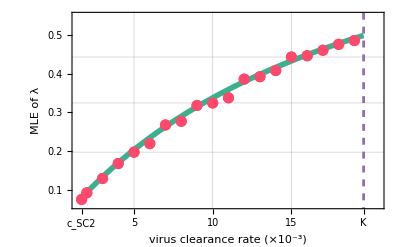

```mathematica
curvePlot=Plot[1/(1+(vrrrangemax/x)),{x,1.44,vrrrangemax},
PlotLabel->"The MLE estimates shown against a Hill curve with n=1",
AxesLabel->{"μ","MLE of λ"},
PlotStyle->{ColorData["Crayola"]["JungleGreen"],Thickness[0.010]},PlotRange->{0,0.55}];
Show[ p3,curvePlot,p3]
```

Observation nr2: at this point we have a concave function.

## Branching processes: the theoretical PoE

Using the above observation regarding a reasonable fit to geometrical distribution, the PoE is given by the fix point of the PGF of the geometrical distribution.

The POE is given by

G_X(q)=q
q / (1 - (1-q)x) = x, thus we have
q = x * (1 - (1-q)x) 

We have a simple second order equation. The non-negative solution to that is:

```mathematica
POE[q_]:=N[(1-Sqrt[1-4*(1-(q))*(q)])/(2*(1-(q)))]
```

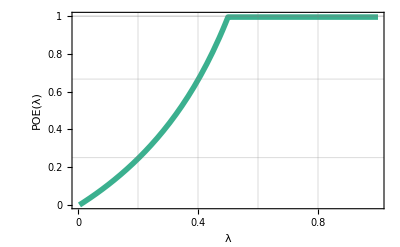

```mathematica
Plot[
N[(1-Sqrt[1-4*(1-(q))*(q)])/(2*(1-(q)))]-0.005,{q,0,1},
PlotStyle->{ColorData["Crayola"]["JungleGreen"],Thickness[0.010]},
FrameLabel->{Row[{Style["λ", 28]}],"POE(λ)"},PlotTheme->"Scientific",LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
PlotRange->{{0,1.0},{0,1.00}},
TicksStyle->Small,
GridLines->{{0.2,0.4,0.6,0.8}, Map[POE[#] &, {0.2,0.4,0.6,0.8}]},
FrameTicks->{
{{{0, "0   "},0.2,0.4,0.6,0.8,{1, "1   "}},None},
{{0,0.2,0.4,0.6,0.8,1},None}},
ImageSize->Scaled[0.6]]
```

We have seen that q = q(mu), where we found that q = q(mu) takes the following form: q(mu) = 1 / (1 + 19.27/mu)

Altogether we have

q / (1 - (1-q)x) = x and
q(mu) = 1 / (1 + 19.27/mu)

The probability of extinction is given (below on the LHS) as a function of q (the relative frequency of 0 offsprings), and for that to be a linear function of mu we need the following:

```mathematica
Solve[(1-Sqrt[1-4*(1-q)*q])/(2*(1-q))==(1/c)*mu,q]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{q→mu/(c+mu)}}

Which corresponds to what we have previously observed.

## Theoretical linearity

```mathematica
PoE[q_]:=(1-Sqrt[1-4*(1-q)*q])/(2*(1-q))
```

```mathematica
qMLE[mu_]:=1/(1 + (vrrrangemax)/mu)
```

```mathematica
POEqMLE={{0.5,PoE[qMLE[0.5]]},{1.0,PoE[qMLE[1.0]]},{2.0,PoE[qMLE[2.0]]},{3,PoE[qMLE[3.0]]},{4,PoE[qMLE[4.0]]},{5,PoE[qMLE[5]]},{6,PoE[qMLE[6]]},{7,PoE[qMLE[7]]},{8,PoE[qMLE[8]]},{9,PoE[qMLE[9]]},{10,PoE[qMLE[10]]},{11,PoE[qMLE[11]]},{12,PoE[qMLE[12]]},{13,PoE[qMLE[13]]},{14,PoE[qMLE[14]]},{15,PoE[qMLE[15]]},{16,PoE[qMLE[16]]},{17,PoE[qMLE[17]]},{18,PoE[qMLE[18]]},{19,PoE[qMLE[19]]},{20,PoE[qMLE[20]]}};
```

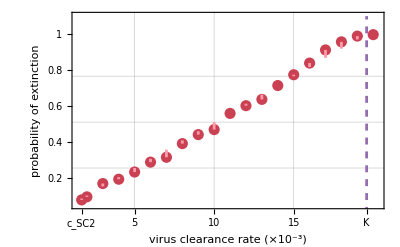

```mathematica
lineStyle={Thickness[0.005],ColorData["Crayola"]["Purple"],Dashed};
lineK=Line[{{vrrrangemax,0},{vrrrangemax,1.1}}];
finalListPlot=ListPlot[
experimentalList,
PlotStyle->{ColorData["Crayola"]["BrickRed"],PointSize[0.02]},
FrameLabel->{Row[{"virus clearance rate   (", Style["×10^-3", 28],")"}],"probability of extinction"},PlotTheme->"Scientific",LabelStyle->Directive[FontFamily->"Times",Black,FontSize->38],
PlotRange->{{1.44,20.3},{0.05,1.1}},
TicksStyle->Medium,
GridLines->{{5,10,15}, Map[PoE[qMLE[#] ]&, {5,10,15}]},
FrameTicks->{
{{ {0, "0   "}, 0.2, 0.4, 0.6, 0.8, {1, "1   "}},None},
{{{1.67, Subscript["c","SC2"]},5,10,15, {vrrrangemax, "K"}},None}},
Epilog->{{Directive[lineStyle],lineK},{Directive[{Thickness[0.005],ColorData["Crayola"]["Salmon"]}],Tooltip[Line[{#,{#[[1]],PoEqMLE[#[[1]]]}}],#[[2]]-PoEqMLE[#[[1]]]]&/@experimentalListForErrorPlot}},
ImageSize->Scaled[0.7]]
```

```mathematica
PoEqMLE[x_]:=PoE[qMLE[x]]
```

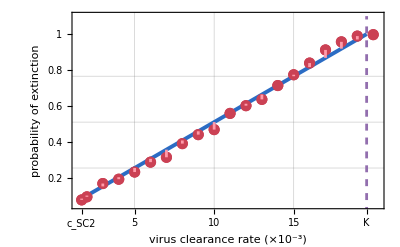

```mathematica
finalPlot=Show[finalListPlot,
Plot[PoEqMLE[x],{x,1.44,vrrrangemax},PlotStyle->{ColorData["Crayola"]["Denim"],Thickness[0.007]}],finalListPlot]
```